LexicalCases Overview |

Installationpaclet:FaizonZaman/LexicalCases/tutorial/LexicalCasesOverview#580651078 | Built-in String Functionspaclet:FaizonZaman/LexicalCases/tutorial/LexicalCasesOverview#323829644
Introductionpaclet:FaizonZaman/LexicalCases/tutorial/LexicalCasesOverview#652844990 | Conclusionpaclet:FaizonZaman/LexicalCases/tutorial/LexicalCasesOverview#2118948183
Searching Files and Servicespaclet:FaizonZaman/LexicalCases/tutorial/LexicalCasesOverview#156924819 |

Installation

This paclet is hosted on the Wolfram Paclet Repositoryhttps://resources.wolframcloud.com/PacletRepository/. First install the paclet from the ResourceObjectpaclet:ref/ResourceObject, then load it with Needspaclet:ref/Needs.

Install the paclet and load its definitions with Needs

```mathematica
PacletInstall[ResourceObject["FaizonZaman/LexicalCases"]];
Needs["FaizonZaman`LexicalCases`"]
```

Introduction

Where StringCasespaclet:ref/StringCases aims for character patterns and TextCasespaclet:ref/TextCases for text patterns, LexicalCases aims for lexical patterns. This is accomplished by expanding the scope of StringExpression where types can be expressed anywhere within. Listed below are the pattern types one can use when searching at the lexical level.

TextTypepaclet:FaizonZaman/LexicalCases/ref/TextTypeFaizonZaman Package Symbol["type"] | Represents a TextContentTypepaclet:guide/TextContentTypes
BoundTokenpaclet:FaizonZaman/LexicalCases/ref/BoundTokenFaizonZaman Package Symbol["string"] | Represents a string with explicit boundaries
BoundTokenpaclet:FaizonZaman/LexicalCases/ref/BoundTokenFaizonZaman Package Symbol[s__1|…|s__i] | Represents any of the s__i with explicit boundaries
WordTokenpaclet:FaizonZaman/LexicalCases/ref/WordTokenFaizonZaman Package Symbol[n] | Represents n words separated by whitespace
Sandwichpaclet:FaizonZaman/LexicalCases/ref/SandwichFaizonZaman Package Symbol[bread, expr] | Sandwiches expr with bread
OptionalTokenpaclet:FaizonZaman/LexicalCases/ref/OptionalTokenFaizonZaman Package Symbol[p] | Represents an optional pattern

Additional pattern constructs made available by the LexicalCases paclet.

Here we can search the Origin Of Species for adverb~adjective patterns ending with "specie" or "species".

Search the origin of species for a lexical pattern

```mathematica
oosp = ExampleData[{"Text","OriginOfSpecies"}];
```

```mathematica
ols=LexicalCases[oosp, TextType["Adverb"]~~TextType["Adjective"]~~BoundToken["specie"|"species"]]
```

LexicalSummary[…]

LexicalCasespaclet:FaizonZaman/LexicalCases/ref/LexicalCasesFaizonZaman Package Symbol returns a LexicalSummarypaclet:FaizonZaman/LexicalCases/ref/LexicalSummaryFaizonZaman Package Symbol object which supports several properties.

"Data" | Returns a list of Associations which contain the match and related metadata like string position
"Dataset" | Returns "Data" as a Datasetpaclet:ref/Dataset
"Counts" | Returns a Datasetpaclet:ref/Dataset  of matches and their counts
"CountGroups" | Returns a Datasetpaclet:ref/Dataset of matches grouped by their count
"CountGroupPercentages" | Returns "CountGroups" with the count replaced by percentage
"PartOfSpeechGroups" | Returns a Datasetpaclet:ref/Dataset of unique words in matches grouped by POS
"WordStemGroups" | Returns a Datasetpaclet:ref/Dataset of unique words in matches grouped by word stem
"Source" | Returns a string indicating whether the source is "Wikipedia" or "Text"
"TotalMatchCount" | Returns the total number of matches found
"LexicalStructure" | Returns a text structure diagram of the lexical pattern
"Survey" | Returns a Dashboard of results

LexicalSummary properties

View the list of properties.

```mathematica
ols["Properties"]
```

{Data,Dataset,Counts,CountGroups,CountGroupPercentages,LowercaseCountGroupPercentages,PartOfSpeechGroups,WordStemCountGroups,Source,TotalMatchCount,LexicalStructure,Survey}

Use the "Data" and "Dataset" properties to extract the results from the summary object.

View search results in a Datasetpaclet:ref/Dataset.

```mathematica
ols["Dataset"]
```

Use "Counts" to view the frequency of matches, or use "CountGroups" to group matches by frequency.

Return a dataset of matches grouped by their count

```mathematica
ols["CountGroups"]
```

"Survey" returns a dashboard of selected properties.

Return a Survey of results

```mathematica
ols["Survey"]
```

Note that "Survey" returns a lexical dispersion plot. This plot is not exclusive to the survey property, there are two other ways to produce it . Either use the "LexicalDispersion" property, or use the LexicalDispersionPlotpaclet:FaizonZaman/LexicalCases/ref/LexicalDispersionPlotFaizonZaman Package Symbol function.

Quickly get a lexical dispersion plot from a summary object

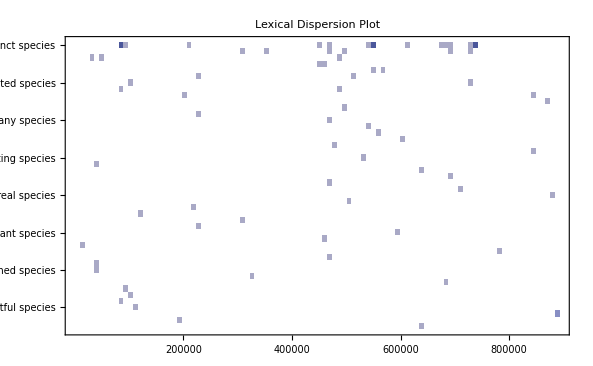

```mathematica
ols["LexicalDispersion"]
```

There are a lot of examples in this plot, there may be cases where one wants to reduce that number. Some properties of a LexicalSummary can be filtered using the MaxItems or DeleteStopwords property options.

Display just 5 examples

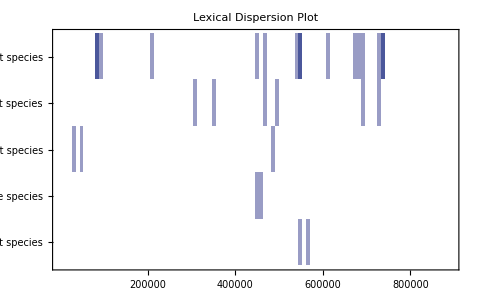

```mathematica
ols["LexicalDispersion",MaxItems->5]
```

As previously mentioned one can also use the LexicalDispersionPlotpaclet:FaizonZaman/LexicalCases/ref/LexicalDispersionPlotFaizonZaman Package Symbol function. This function takes a string or list of strings as its first argument (the source) and a list of strings or lexical patterns as its second argument. In the case that multiples sources are given, multiple plots are returned. Set the DataJoin option to Truepaclet:ref/True to return a single plot.

Get a lexical dispersion plot of the 5 most common bigrams in the origin of species

```mathematica
bgrams=WordCounts[oosp,2][[;;5]]//Keys//Map[StringRiffle]
```

{of the,in the,the same,to the,on the}

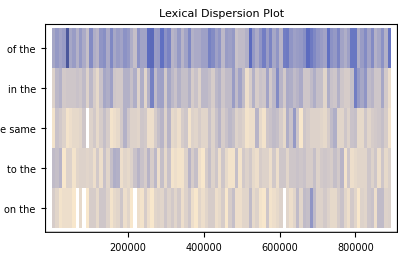

```mathematica
LexicalDispersionPlot[oosp,bgrams]
```

LexicalDispersionPlot supports lexical patterns as well.

Get a lexical dispersion plot of lexical patterns in the Origin of Species

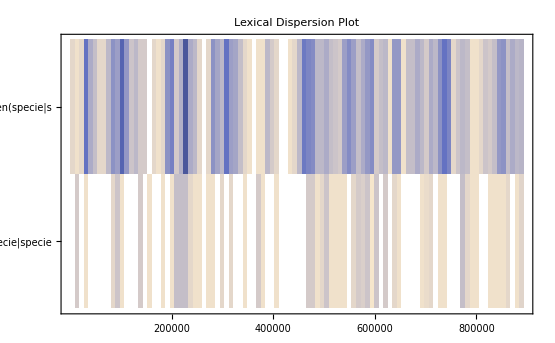

```mathematica
LexicalDispersionPlot[oosp,{
TextType["Adjective"]~~BoundToken["specie"|"species"],
TextType["Noun"]~~BoundToken["specie"|"species"]
}
]
```

For more information on LexicalDispersionPlotpaclet:FaizonZaman/LexicalCases/ref/LexicalDispersionPlotFaizonZaman Package Symbol see the documentation.

Searching Files and Services

### Services — Wikipedia

It's nice to be able to search strings, but one may want more data to search over. Using a "Content" or "Category" rule, or just a lexical pattern itself as input will search over Wikipedia. The MaxItemspaclet:ref/MaxItems option will restrict the number of articles collected. Note that when LexicalCases is given just a lexical pattern, and no source text, an attempt is made to convert the pattern to a Wikipedia search query, which might not always work.

Search over Wikipedia articles containing the keyword "science fiction"

```mathematica
scifi=LexicalCases["Content"->"science fiction",WordToken[1,"KeepContractions"]~~"car",MaxItems->1000];
```

```mathematica
scifi["CountGroups"]
```

There is potential for lexical patterns to become quite unwieldy, making them potentially difficult to read.  The "Structure" property of a LexicalSummary object, or the LexicalStructurepaclet:FaizonZaman/LexicalCases/ref/LexicalStructureFaizonZaman Package Symbol function applied to a lexical pattern, might help clarify the pattern's structure.

View a lexical pattern's structure

```mathematica
scifi["LexicalStructure"]
```

1
WordToken  car
Text
StringExpression

```mathematica
LexicalStructure[TextType["Verb"]~~"car"~~OptionalToken[BoundToken["price"|"prices"]]]
```

Verb
TextType  car
Text        price
Text|  prices
Text
Alternatives
BoundToken
Optional
StringExpression

### Files

LexicalCasespaclet:FaizonZaman/LexicalCases/ref/LexicalCasesFaizonZaman Package Symbol supports Filepaclet:ref/File objects, File paths and SearchIndexObjectpaclet:ref/SearchIndexObject's as input. If using a file-path string, surround it with either Filepaclet:ref/File or Listpaclet:ref/List. SearchIndexObjectpaclet:ref/SearchIndexObject's allow one to search over files in a particular set of directories. Use CreateSearchIndexpaclet:ref/CreateSearchIndex to make one. In LexicalCasespaclet:FaizonZaman/LexicalCases/ref/LexicalCasesFaizonZaman Package Symbol specify which files to use from the index by supplying a search query. This is done with a Rulepaclet:ref/Rule where the left-hand-side (lhs) is the index and the right-hand-side (rhs) is the search query.  A Stringpaclet:ref/String or SearchQueryStringpaclet:ref/SearchQueryString is valid rhs.

Built-in String Functions

If you prefer lightweight output, instead of the LexicalSummarypaclet:FaizonZaman/LexicalCases/ref/LexicalSummaryFaizonZaman Package Symbol object, consider using the LexicalPatternpaclet:FaizonZaman/LexicalCases/ref/LexicalPatternFaizonZaman Package Symbol wrapper with native String functions (Note: options are not supported at the moment).

Get example text

```mathematica
alice = ExampleData[{"Text","AliceInWonderland"}];
```

```mathematica
aliceVerbAdverbPattern=LexicalPattern["Alice"~~TextType["Verb"]~~TextType["Adverb"]];
```

Find cases of aliceVerbAdverbPattern in "Alice In Wonderland"

```mathematica
StringCases[alice, aliceVerbAdverbPattern]
```

{Alice had not,Alice was not,Alice's first,Alice went back,Alice took up,Alice had no,Alice was soon,Alice could only,Alice looked all,Alice could not,Alice was more,Alice crouched down,Alice went timidly,Alice was just,Alice looked down,Alice had not,Alice got up,Alice was very,Alice looked up,Alice was too,Alice got up}

Find string positions of aliceVerbAdverbPattern matches in "Alice In Wonderland"

```mathematica
StringPosition[alice, aliceVerbAdverbPattern]
```

{{1349,1361},{2548,2560},{3456,3468},{4360,4374},{8488,8500},{16084,16095},{18290,18303},{22528,22543},{25145,25160},{26380,26394},{29462,29475},{30448,30466},{32290,32307},{35021,35034},{35170,35186},{36142,36154},{38307,38318},{43702,43715},{44556,44570},{44958,44970},{51619,51630}}

Check if a string matches aliceVerbAdverbPattern

```mathematica
StringMatchQ["Alice walked quickly", aliceVerbAdverbPattern]
```

True

It's also possible to use the operator forms of these functions.

Define a Q operator for matching a lexical pattern

```mathematica
aliceVerbAdverbQ=StringMatchQ[aliceVerbAdverbPattern];
```

```mathematica
aliceVerbAdverbQ["Alice walked quickly"]
```

True

Conclusion

LexicalCases provides a set of lexical pattern objects, a way to query them on strings, files, and large datasets like Wikipedia articles, and easy access to properties of results. Additionally, one can use LexicalDispersionPlotpaclet:FaizonZaman/LexicalCases/ref/LexicalDispersionPlotFaizonZaman Package Symbol to see how these structures are used across a text. With this paclet, I hope lexical researchers and enthusiasts can easily explore lexical patterns in a consistent, wolfram language way. Feedback is welcome! Please send a message on the paclet repository, or visit the GitHubhttps://github.com/dishmint/LexicalCases repository.

| Related Guides
▪LexicalCasesOverview